```mathematica
SetDirectory["~/Dropbox/personal/projects/mathca/cpi"]
```

/home/adam/Dropbox/personal/projects/mathca/cpi

```mathematica
cpi=Flatten[Import["cpi.csv"]];
```

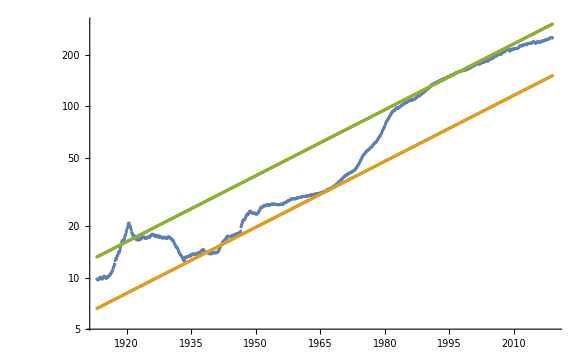

```mathematica
{{1913+#/12,cpi[[#]]}&/@Range[Length[cpi]],{1913+#/12,6.6*1.03^(#/12)}&/@Range[Length[cpi]],{1913+#/12,6.6*2*1.03^(#/12)}&/@Range[Length[cpi]]}//ListLogPlot
```

```mathematica
ListLogPlot[{{1913+#/12,cpi[[#]]/1.03^(#/12)}&/@Range[Length[cpi]]}]
```

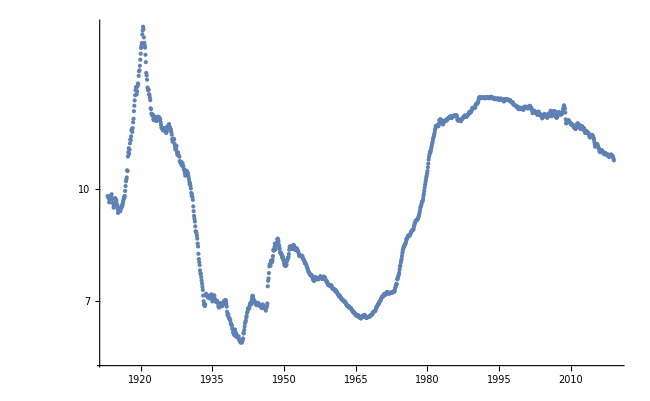

```mathematica
1.03*2^.1
```

1.10393

```mathematica
Log[2]/Log[1.03]
```

23.4498